```mathematica
(*Definiujemy stałe astronomiczne*)G=6.674*10^-11;(*stała grawitacyjna*)M=1.989*10^30;(*masa Słońca*)(*Definiujemy parametry orbity planety*)a=1.496*10^11;(*półoś wielka orbity w metrach*)e=0.0167;(*mimośród orbity*)T=365.25636*24*3600;(*okres orbitalny w sekundach*)(*Obliczamy półoś małą orbity*)b=a*Sqrt[1-e^2];

(*Definiujemy funkcję r(t),która określa położenie planety w czasie t*)
r[t_]:={(a*(Cos[2*Pi/T*t]-e)),(b*Sin[2*Pi/T*t]),0};

(*Generujemy wykres orbity planety*)
ParametricPlot3D[r[t],{t,0,T},PlotStyle->{Blue,Thickness[0.01]},AxesLabel->{"x","y","z"},PlotRange->All,ImageSize->500]
```

-Graphics3D-

```mathematica
(*Zdefiniuj datę*)data={{"Mercury",0.387},{"Venus",0.723},{"Earth",1.000},{"Mars",1.523},{"Jupiter",5.202},{"Saturn",9.539},{"Uranus",19.18},{"Neptune",30.06}};

(*Oblicz odległości od Słońca*)
distanceFromSun=data[[All,2]];

(*Narysuj dane*)
ListPointPlot3D[data,AxesLabel->{"Planet","Distance from Sun (AU)"},PlotLabel->"Planet Distances from the Sun"]
```

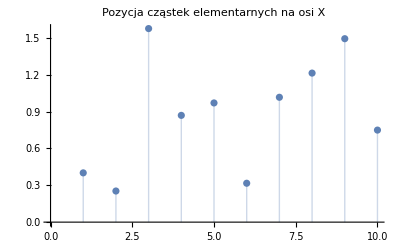

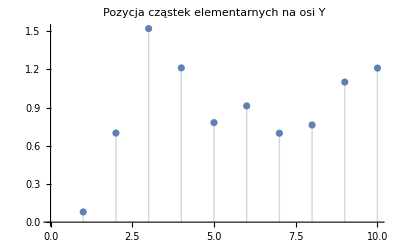

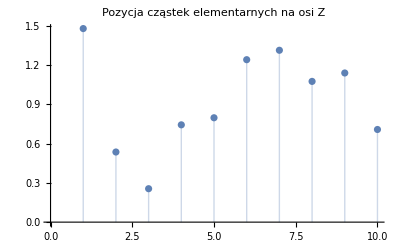

```mathematica
(*Ustawienia początkowe*)n=10;(*Liczba cząstek elementarnych*)R=Table[RandomReal[],{n},{3}];(*Początkowa pozycja cząstek elementarnych*)V=Table[RandomReal[],{n},{3}];(*Początkowa prędkość cząstek elementarnych*)(*Symulacja cząstek elementarnych*)(*Określenie czasu trwania symulacji*)tmax=100;(*Maksymalny czas trwania symulacji*)dt=0.01;(*Krok symulacji*)(*Petla symulacyjna*)For[t=0,t<tmax,t=t+dt,R=R+V*dt;(*Aktualizacja pozycji cząstek elementarnych*)V=V-V*dt;(*Aktualizacja prędkości cząstek elementarnych*)];

(*Wykresy*)
(*Wykres pozycji cząstek elementarnych na osi X*)
ListPlot[R[[All,1]],Filling->Axis,PlotLabel->"Pozycja cząstek elementarnych na osi X"]

(*Wykres pozycji cząstek elementarnych na osi Y*)
ListPlot[R[[All,2]],Filling->Axis,PlotLabel->"Pozycja cząstek elementarnych na osi Y"]

(*Wykres pozycji cząstek elementarnych na osi Z*)
ListPlot[R[[All,3]],Filling->Axis,PlotLabel->"Pozycja cząstek elementarnych na osi Z"]
```